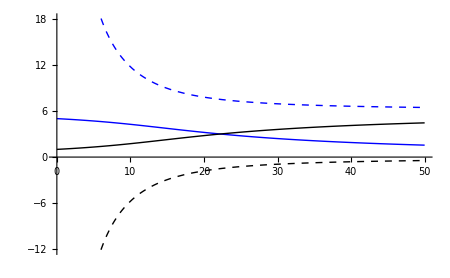

```mathematica
Module[{k,vo,Ca0,Cb0,s},
k=0.1;
vo=10;
Ca0=5;
Cb0=1;

s:=Quiet@Solve[0==vo*Ca0-vo*Ca-k*Ca*Cb*V∧0==vo*Cb0-vo*Cb+k*Ca*Cb*V,{Ca,Cb}];

Plot[{Evaluate[Ca/.s[[1]]],Evaluate[Ca/.s[[2]]],Evaluate[Cb/.s[[1]]],Evaluate[Cb/.s[[2]]]},{V,0,50},PlotStyle->{{Thick,Blue},{Thick,Blue,Dashed},{Thick,Black},{Thick,Black,Dashed}},ImageSize->450]
]
```

In the plot above, I solved the two equations you wrote out yesterday for an autocatalytic reaction in a CSTR. I did see an error in your equations (you subtracted k C_A C_B V from both when it should have been added to the balance for the product) and corrected it. This is what I got when I re-wrote the calculations in “eq1”. There have always been 4 solutions but we have been plotting the wrong ones (dotted).

Equations used in “eq1” notebook:

Rate of reaction:
	first order:		-r_A=k C_A
	autocatalytic:	-r_A=k C_A C_B
For a CSTR I solved these two equations simultaneously to get C_A and C_B, reactant and product concentrations:
	V=vo (C_(A,0)-C_A)/-r_A,
	V=vo (C_(B,0)-C_B)/r_A.
For the PFR I solved the differential equaitons:
	(ⅆ C_A)/ⅆV=r_A/vo,
	(ⅆ C_B)/ⅆV=-r_A/vo.

This is basically what Garrison had but he solved the CSTR equations by hand. There are 2 solutions for C_A and C_B for an autocatalytic reaction in a CSTR, I used the other solution.